# Condensate+Waves (All Order terms)

#### For simplifying EOM

```mathematica
s={{1,0,0},{0,1,0}};nv={0,0,1};
```

```mathematica
Qaik={{{1,0,0},{0,-1,0},{0,0,0}},{{0,1,0},{1,0,0},{0,0,0}}};
```

```mathematica
Qaik[[1]]//MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Qaik[[2]]//MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Table[Sum[Qaik[[γ]][[l]][[k]]Qaik[[α]][[l]][[i]]Qaik[[β]][[p]][[k]]Qaik[[δ]][[p]][[i]] Subscript[AA, α] Subscript[AA, β] Subscript[AA, δ],{α,1,2},{β,1,2},{δ,1,2},{l,1,3},{i,1,3},{k,1,3},{p,1,3}],{γ,1,2}]
```

{2 AA_1^3+2 AA_1 AA_2^2,2 AA_1^2 AA_2+2 AA_2^3}

```mathematica
coord={x,y,z};
```

```mathematica
Sum[Normal[LeviCivitaTensor[3]][[a]][[c]][[i]]Qaik[[α]][[c]][[k]]Qaik[[β]][[a]][[k]]Subscript[AA, α][t,z]D[Subscript[AA, β][t,z],coord[[i]]],{α,1,2},{β,1,2},{a,1,3},{i,1,3},{c,1,3},{k,1,3}]
```

2 AA_2[t,z] AA_1^(0,1)[t,z]-2 AA_1[t,z] AA_2^(0,1)[t,z]

## Using NDSolve

```mathematica
g=0.5;
eqn={U''[t]+2 g^2 U[t]^3+2 g/3(V[t,z]D[W[t,z],z]-W[t,z]D[V[t,z],z])==0,-D[V[t,z],t,t]+D[V[t,z],z,z]-2 g U[t] D[W[t,z],z]+2 g^2(V[t,z]^2+2V[t,z]W[t,z]-W[t,z]^2)-2 g^2(W[t,z]^2+V[t,z]^2)V[t,z]==0,
-D[W[t,z],t,t]+D[W[t,z],z,z]+2 g U[t] D[V[t,z],z]-2 g^2(V[t,z]^2-2V[t,z]W[t,z]+W[t,z]^2)-2 g^2(W[t,z]^2+V[t,z]^2)W[t,z]==0};
ic={U[0]==1,V[0,z]==0.01,W[0,z]==0.01};
bc={D[U[t],t]==0/.t->0,D[V[t,z],t]==0/.t->0,D[W[t,z],t]==0/.t->0,D[V[t,z],z]==0/.z->0,D[W[t,z],z]==0/.z->0};
```

```mathematica
sol=NDSolve[{eqn,ic,bc},{U,V,W},{t,0,5},{z,0,5},Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->{"Length"->1*^-4}}}}]
```

NDSolve::overdet: There are fewer dependent variables, {V[t,z],W[t,z]}, than equations, so the system is overdetermined.

NDSolve[{{0.5 U[t]^3+U''[t]+0.333333 (-W[t,z] V^(0,1)[t,z]+V[t,z] W^(0,1)[t,z])==0,0.5 (V[t,z]^2+2 V[t,z] W[t,z]-W[t,z]^2)-0.5 V[t,z] (V[t,z]^2+W[t,z]^2)-1. U[t] W^(0,1)[t,z]+V^(0,2)[t,z]-V^(2,0)[t,z]==0,-0.5 W[t,z] (V[t,z]^2+W[t,z]^2)-0.5 (V[t,z]^2-2 V[t,z] W[t,z]+W[t,z]^2)+1. U[t] V^(0,1)[t,z]+W^(0,2)[t,z]-W^(2,0)[t,z]==0},{U[0]==1,V[0,z]==0.01,W[0,z]==0.01},{V^(1,0)[0,z]==0,W^(1,0)[0,z]==0,V^(0,1)[t,0]==0,W^(0,1)[t,0]==0}},{U,V,W},{t,0,5},{z,0,5},Method→{MethodOfLines,SpatialDiscretization→{FiniteElement,MeshOptions→{MaxCellMeasure→{Length→1/10000}}}}]

## Solving using Method of lines

U=U(t);V=ψ_1(t,z);W=ψ_2(t,z);
U_tt+2 g^2 U^3+(2g)/3(∫^Inf)_-Inf(V W_z-W V_z)dz=0;                                                                 ; U_tt=-2 g^2 U^3-(2g)/3(∫^Inf)_-Inf(V W_z-W V_z) dz
-V_tt+V_zz-2g U W_z- g^2(V^2+W^2)V=0;            ;V_tt=V_zz-2g U W_z- g^2(V^2+W^2)V
-W_tt+W_zz+2g U V_z-g^2(V^2+W^2)W=0;     ;W_tt=W_zz+2g U V_z-g^2(V^2+W^2)W

```mathematica
Integrate[1,{x,-5,5}]
```

10

```mathematica
Clear[U,V,W];g=0.5;
```

```mathematica
(*z_initial=zi,z_final=zf ----h, n=(zf-zi)/h*)
```

```mathematica
(*Taking v(z=zi,t)=0.01,v(z=zf,t)=0.01,w(z=zi,t)=0.01,w(z=zf,t)=0.01*)
```

```mathematica
h=0.1;n=IntegerPart[20/h];z0=-10;n
```

200

```mathematica
V[t_]=Table[Subscript[v, i][t],{i,0,n}];
```

```mathematica
W[t_]=Table[Subscript[w, i][t],{i,0,n}];
```

```mathematica
(*Finding integral term in the equation for U *)
```

```mathematica
Int=(1/4)(Subscript[v, 0][t](-3 Subscript[w, 0][t]+4 Subscript[w, 1][t]-Subscript[w, 2][t])-Subscript[w, 0][t](-3 Subscript[v, 0][t]+4 Subscript[v, 1][t]-Subscript[v, 2][t])+Subscript[v, n][t](Subscript[w, n-2][t]-4 Subscript[w, n-1][t]+3 Subscript[w, n][t])-Subscript[w, n][t](Subscript[v, n-2][t]-4 Subscript[v, n-1][t]+3 Subscript[v, n][t])+2Sum[Subscript[v, i][t](Subscript[w, i+1][t]-Subscript[w, i-1][t])-Subscript[w, i][t](Subscript[v, i+1][t]-Subscript[v, i-1][t]),{i,1,n-1}]);
```

```mathematica
(*Making all equations for U, V and W*)
```

```mathematica
eqns=Thread[Flatten[{D[U[t],t,t],D[V[t],t,t],D[W[t],t,t]}]==Join[{-2 g^2 U[t]^3-Int},{0.01},ListCorrelate[1/h^2{1,-2,1},V[t]]-ListCorrelate[g U[t] 1/h{-1,0,1},W[t]]-g^2 Delete[(V[t]^2+W[t]^2)V[t],{{1},{-1}}],{0.01},{0.01},ListCorrelate[1/h^2{1,-2,1},W[t]]+ListCorrelate[g U[t] 1/h{-1,0,1},V[t]]-g^2 Delete[(V[t]^2+W[t]^2)V[t],{{1},{-1}}],{0.01}]];(*With a nonzero ic value and non zero value in right end*)
```

```mathematica
initc=Thread[Flatten[{U[0],U'[0],W[0],V[0],W'[0],V'[0]}]==Join[{1},{0},Table[0.01,{i,0,2n+1}],Table[0,{i,0,2n+1}]]];
```

```mathematica
linessol=NDSolve[{eqns,initc},Flatten[{U[t],W[t],V[t]}],{t,0,15},Method->"StiffnessSwitching"];
```

```mathematica
psi1=Interpolation[Flatten[Table[{{t,z0+i h},First[Subscript[w, i][t]/. linessol]},{i,0,n},{t,0,15}],1],InterpolationOrder->1];
```

```mathematica
psi2=Interpolation[Flatten[Table[{{t,z0+i h},First[Subscript[v, i][t]/. linessol]},{i,0,n},{t,0,15}],1],InterpolationOrder->1];
```

```mathematica
Ut[t_]=U[t]/.linessol[[1]]
```

InterpolatingFunction[…][t]

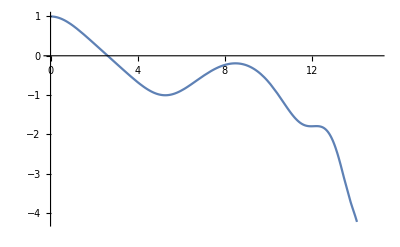

```mathematica
Plot[Ut[t],{t,0,15}]
```

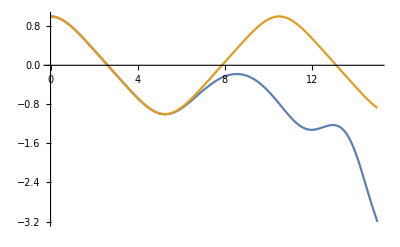

```mathematica
Plot[{Ut[t],JacobiCD[0.5t,-1]},{t,0,15}]
```

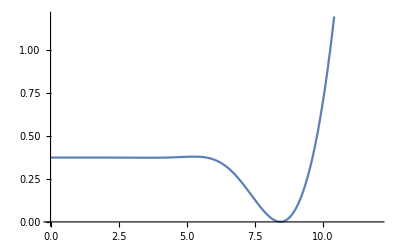

```mathematica
Plot[3/2(d'[t]d'[t]+g^2 d[t]^4),{t,0,12}]
```

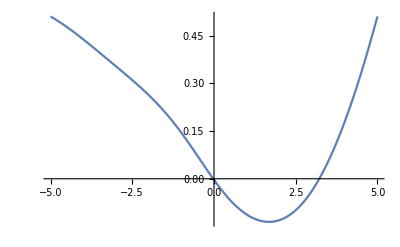

```mathematica
ListPlot[Evaluate[Table[{z0+i h,First[Subscript[w, i][t]/. linessol]/.t->10},{i,0,n}]],Joined->True]
```

```mathematica
ParametricPlot3D[Evaluate[Table[{z0+i h,t,First[Subscript[w, i][t]/. linessol]},{i,0,n}]],{t,0,13},PlotRange->All,AxesLabel->{"z","t","w"}]
```

-Graphics3D-

```mathematica
Plot3D[psi1[t,z],{t,0,15},{z,-10,10},AxesLabel->{t,z,Subscript[ψ, 1]},PlotRange->All,ColorFunction->Function[{z,t,y},Hue[0.7y]]]
```

-Graphics3D-

```mathematica
Plot3D[psi2[t,z],{t,0,15},{z,-10,10},AxesLabel->{t,z,Subscript[ψ, 2]},PlotRange->All,ColorFunction->Function[{z,t,y},Hue[0.7y]]]
```

-Graphics3D-

## Keeping U(t) constant and find ψ_α:

## Using a function

#### Creating a function pdetoode:

```mathematica
Clear[fdd,pdetoode,tooderule,pdetoae,diffbc,rebuild]
fdd[{},grid_,value_,order_,periodic_]:=value;
fdd[a__]:=NDSolve`FiniteDifferenceDerivative@a;

pdetoode[funcvalue_List,rest__]:=pdetoode[(Alternatives@@Head/@funcvalue)@@funcvalue[[1]],rest];
pdetoode[{func__}[var__],rest__]:=pdetoode[Alternatives[func][var],rest];
pdetoode[front__,grid_?VectorQ,o_Integer,periodic_:False]:=pdetoode[front,{grid},o,periodic];

pdetoode[func_[var__],time_,{grid:{__}..},o_Integer,periodic:True|False|{(True|False)..}:False]:=With[{pos=Position[{var},time][[1,1]]},With[{bound=#[[{1,-1}]]&/@{grid},pat=Repeated[_,{pos-1}],spacevar=Alternatives@@Delete[{var},pos]},With[{coordtoindex=Function[coord,MapThread[Piecewise[{{1,PossibleZeroQ[#-#2[[1]]]},{-1,PossibleZeroQ[#-#2[[-1]]]}},All]&,{coord,bound}]]},tooderule@Flatten@{((u:func)|Derivative[dx1:pat,dt_,dx2___][(u:func)])[x1:pat,t_,x2___]:>(Sow@coordtoindex@{x1,x2};
fdd[{dx1,dx2},{grid},Outer[Derivative[dt][u@##]@t&,grid],"DifferenceOrder"->o,PeriodicInterpolation->periodic]),inde:spacevar:>With[{i=Position[spacevar,inde][[1,1]]},Outer[Slot@i&,grid]]}]]];

tooderule[rule_][pde_List]:=tooderule[rule]/@pde;
tooderule[rule_]@Equal[a_,b_]:=Equal[tooderule[rule][a-b],0]//.eqn:HoldPattern@Equal[_,_]:>Thread@eqn;
tooderule[rule_][expr_]:=#[[Sequence@@#2[[1,1]]]]&@@Reap[expr/. rule]

pdetoae[funcvalue_List,rest__]:=pdetoae[(Alternatives@@Head/@funcvalue)@@funcvalue[[1]],rest];
pdetoae[{func__}[var__],rest__]:=pdetoae[Alternatives[func][var],rest];

pdetoae[func_[var__],rest__]:=Module[{t},Function[pde,#[pde/. {Derivative[d__][u:func][inde__]:>Derivative[d,0][u][inde,t],(u:func)[inde__]:>u[inde,t]}]/. (u:func)[i__][t]:>u[i]]&@pdetoode[func[var,t],t,rest]]

diffbc[rst__][a:_List|_Equal]:=diffbc[rst]/@a
diffbc[dvar:{t_,order_}|(t_)..,sf_:0][a_]/;sf=!=t:=sf a+D[a,dvar]

rebuild[funcarray_,grid_?VectorQ,timeposition_:1]:=rebuild[funcarray,{grid},timeposition]

rebuild[funcarray_,grid_,timeposition_?Negative]:=rebuild[funcarray,grid,Range[Length@grid+1][[timeposition]]]

rebuild[funcarray_,grid_,timeposition_:1]/;Dimensions@funcarray===Length/@grid:=With[{depth=Length@grid},ListInterpolation[Transpose[Map[Developer`ToPackedArray@#["ValuesOnGrid"]&,#,{depth}],Append[Delete[Range[depth+1],timeposition],timeposition]],Insert[grid,Flatten[#][[1]]["Coordinates"][[1]],timeposition]]&@funcarray]
```

```mathematica
points=25;
grid=Array[#&,points,{0,1}];
```

## Others

#### Practice

```mathematica
(*Composite trapezoid rule:(∫^b)_a f(x)dx=(b-a)/2(f(a)+2 Subscript[Σ^(n-1), i=1] f(a+ih)+f(b))*)
```

```mathematica
(*example:(∫^1)_0 g'(x)*)
```

```mathematica
G=Table[i^2,{i,0,1,0.01}]
```

{0.,0.0001,0.0004,0.0009,0.0016,0.0025,0.0036,0.0049,0.0064,0.0081,0.01,0.0121,0.0144,0.0169,0.0196,0.0225,0.0256,0.0289,0.0324,0.0361,0.04,0.0441,0.0484,0.0529,0.0576,0.0625,0.0676,0.0729,0.0784,0.0841,0.09,0.0961,0.1024,0.1089,0.1156,0.1225,0.1296,0.1369,0.1444,0.1521,0.16,0.1681,0.1764,0.1849,0.1936,0.2025,0.2116,0.2209,0.2304,0.2401,0.25,0.2601,0.2704,0.2809,0.2916,0.3025,0.3136,0.3249,0.3364,0.3481,0.36,0.3721,0.3844,0.3969,0.4096,0.4225,0.4356,0.4489,0.4624,0.4761,0.49,0.5041,0.5184,0.5329,0.5476,0.5625,0.5776,0.5929,0.6084,0.6241,0.64,0.6561,0.6724,0.6889,0.7056,0.7225,0.7396,0.7569,0.7744,0.7921,0.81,0.8281,0.8464,0.8649,0.8836,0.9025,0.9216,0.9409,0.9604,0.9801,1.}

```mathematica
Length[G]
```

101

```mathematica
1/4 ((-3G[[1]]+4G[[2]]-G[[3]])+(G[[99]]-4G[[100]]+3G[[101]])+2Sum[(G[[i+1]]-G[[i-1]]),{i,2,100}])
```

```mathematica
1/4 ((-3G[[1]]+4G[[2]]-G[[3]])+(G[[99]]-4G[[100]]+3G[[101]])+2Sum[(G[[i+1]]-G[[i-1]]),{i,2,100}])
```

1.